Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

2 - 11 Line integral. Work.
Calculate ∫_C F(r).ⅆr for the given data. If F is a force, this gives the work done by the force in the displacement along C.

2.  F={y^2,-x^2}, C:y=4 x^2  from {0, 0} to {1, 4}

```mathematica
ClearAll["Global`*"]
```

Above: on line I found that the standard parameterization of the parabola x^2= 4 a y is x=2 a t, y=a t^2.

The first task is parameterization of the path.

```mathematica
Solve[1/4 y==4 a y]
```

{{a→1/16},{y→0}}

```mathematica
p[t_]={t/8,t^2/16}
```

{t/8,t^2/16}

Above: it can be seen that t will run from 0 to 8. Now to define the vector field:

```mathematica
ff[{x_,y_}]={y^2,-x^2}
```

{y^2,-x^2}

Below: then evaluate the field along the path:

```mathematica
e1=ff[p[t]]
```

{t^4/256,-t^2/64}

Below: dot the last vector russian doll with the derivative of the position function.

```mathematica
e2=e1.p'[t]
```

-t^3/512+t^4/2048

Below: and then do the integration,

```mathematica
e3=Integrate[e2,{t,0,8}]
```

6/5

Problem 2 is not odd, so there is no answer in the appendix.

3.  F as in problem 2. C from {0, 0} straight to {1, 4}. Compare.

```mathematica
ClearAll["Global`*"]
```

Again, the first step is parameterization. To parameterize a straight line from P to Q means a function r(t)=(1-t)P+t Q. In the present case that would be

```mathematica
r[t_]=(1-t) {0,0}+t{1,4}
```

{t,4 t}

Above: it can be seen that t will run from 0 to 1. Now to define the vector field:

```mathematica
ff[{x_,y_}]={y^2,-x^2}
```

{y^2,-x^2}

Above: using the same vector field equation as in the last problem. Below: then evaluate the field along the path:

```mathematica
e1=ff[r[t]]
```

{16 t^2,-t^2}

Below: dot the last chinese fortune cookie with the derivative of the position function.

```mathematica
e2=e1.r'[t]
```

12 t^2

Below: and then do the integration,

```mathematica
e3=Integrate[e2,{t,0,1}]
```

4

The problem description wanted to have problem 2 and 3 compared. Problem 2 is blue, problem 3 is red.

```mathematica
plot1=ParametricPlot[{16 t^2,-t^2},{t,0,1},PlotRange->{{-5,20},{-2,2}},PlotStyle->{Red,Thickness[0.002]},AspectRatio->.3];
```

```mathematica
plot2=ParametricPlot[{t^4/256,-t^2/64},{t,0,8},PlotRange->{{-5,20},{-2,2}},PlotStyle->{Blue,Thickness[0.002]},AspectRatio->.3];
```

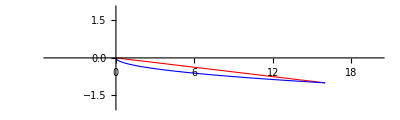

```mathematica
Show[plot1,plot2]
```

Above: something odd here. It seems obvious that blue is longer than red, but the integral comes out smaller. Knowing that the line integral does not measure the length of the line, it is still a hard concept to accept.

4.  F={xy,x^2 y^2}, C from {2, 0} straight to {0, 2}

5.  F as in problem 4. C the quarter-circle from {2, 0} to {0, 2} with center {0, 0}

```mathematica
ClearAll["Global`*"]
```

First the parameterization, which should be easy.

```mathematica
r[t_]={2 Cos[t],2Sin[t]}
```

{2 Cos[t],2 Sin[t]}

Above: t will run from 0 to π/2. Now to define the vector field:

```mathematica
ff[{x_,y_}]={x y,x^2 y^2}
```

{x y,x^2 y^2}

Below: then evaluate the field along the path:

```mathematica
e1=ff[r[t]]
```

{4 Cos[t] Sin[t],16 Cos[t]^2 Sin[t]^2}

Below: then dot the multi-level function just calculated with the derivative of the position function,

```mathematica
e2=e1.r'[t]
```

-8 Cos[t] Sin[t]^2+32 Cos[t]^3 Sin[t]^2

Below: and then do the integration:

```mathematica
e3=Integrate[e2,{t,0,π/2}]
```

8/5

7.  F={x^2,y^2,z^2}, C:r={Cos[t],Sin[t], ⅇ^t} from {1,0, 1} to {1, 0, ⅇ^(2π)}. Sketch C.

```mathematica
ClearAll["Global`*"]
```

Here the function r is given. It is apparent that t will run from 0 to 2π.

```mathematica
r[t_]={Cos[t],Sin[t],ⅇ^t}
```

{Cos[t],Sin[t],ⅇ^t}

Below: and the vector field:

```mathematica
ff[{x_,y_,z_}]={x^2,y^2,z^2}
```

{x^2,y^2,z^2}

Below: I need to run the field function along the path:

```mathematica
e1=ff[r[t]]
```

{Cos[t]^2,Sin[t]^2,ⅇ^(2 t)}

Below: and then dot the multi-level with the derivative of the position function:

```mathematica
e2=e1.r'[t]
```

ⅇ^(3 t)-Cos[t]^2 Sin[t]+Cos[t] Sin[t]^2

Below: And then do the integration:

```mathematica
Integrate[e2,{t,0,2 π}]
```

1/3 (-1+ⅇ^(6 π))

```mathematica
plot2=ParametricPlot3D[{Cos[t],Sin[t],ⅇ^t},{t,0,2 π},PlotRange->{{0,1.5},{0,1.5},{.5,5}},PlotStyle->{Blue,Thickness[0.002]},BoxRatios->{1,1,4},ImageSize->150,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

9.  F = {x + y, y + z, z + x}, C : r = {2 t, 5 t, t} from t = 0 to 1. Also from t = -1 to 1.

```mathematica
ClearAll["Global`*"]
```

Another one where the parameterization is already done for me.

```mathematica
r[t_]={2 t,5 t,t}
```

{2 t,5 t,t}

The limits on t are set in the problem.

```mathematica
ff[{x_,y_,z_}]={x+y,y+z,z+x}
```

{x+y,y+z,x+z}

Below: run the field function along the path:

```mathematica
e1=ff[r[t]]
```

{7 t,6 t,3 t}

Below: and dot the result with the derivative of the position function:

```mathematica
e2=e1.r'[t]
```

47 t

Below: and then do the integration:

```mathematica
e3=Integrate[e2,{t,0,1}]
```

47/2

```mathematica
e4=Integrate[e2,{t,-1,1}]
```

0

```mathematica
plot2=ParametricPlot3D[{2 t,5 t,t},{t,0,1},PlotRange->{{-3,4},{-2 π,2 π},{-π,4}},PlotStyle->{Blue,Thickness[0.002]},BoxRatios->{1,1,1},ImageSize->200,AxesLabel->{"x","y","z"}];
```

```mathematica
plot3=ParametricPlot3D[{2 t,5 t,t},{t,-1,1},PlotRange->{{-3,4},{-2 π,2 π},{-π,4}},PlotStyle->{Red,Thickness[0.02],Opacity[.3]},BoxRatios->{1,1,1},ImageSize->200,AxesLabel->{"x","y","z"}];
```

```mathematica
Show[plot2,plot3]
```

-Graphics3D-

Above: the shorter range of t is within.

11.  F={ⅇ^-x,ⅇ^-y,ⅇ^-z}, C:r={t,t^2,t} from {0,0,0} to {2,4,2}. Sketch C.

```mathematica
ClearAll["Global`*"]
```

Here again, the parameterization is taken care of in the problem statement. The position function:

```mathematica
r[t_]={t,t^2,t}
```

{t,t^2,t}

t will go from 0 to 2. Defining the vector field:

```mathematica
ff[{x_,y_,z_}]={ⅇ^-x,ⅇ^-y,ⅇ^-z}
```

{ⅇ^-x,ⅇ^-y,ⅇ^-z}

feeding the vector field through the position function:

```mathematica
e1=ff[r[t]]
```

{ⅇ^-t,ⅇ^(-t^2),ⅇ^-t}

dotting the previous step with the derivative of the position function:

```mathematica
e2=e1.r'[t]
```

2 ⅇ^-t+2 ⅇ^(-t^2) t

performing the integration:

```mathematica
e3=Integrate[e2,{t,0,2}]
```

3-1/ⅇ^4-2/ⅇ^2

Above: this answer matches the second part of the text answer. It is the line length.

```mathematica
plot2=ParametricPlot3D[{t,t^2,t},{t,0,2 π},PlotRange->{{0,8},{0,50},{0,8}},PlotStyle->{Blue,Thickness[0.002]},BoxRatios->{1,1,1},ImageSize->150,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

15 - 20 Integrals (8) and (8*)
These would refer to numbered lines (8) and (8*) on p. 417. Evaluate them with F or f and C as follows.

15.  F={y^2,z^2,x^2}, C:r={3Cos[t],3Sin[t],2t},0≤t≤4π

```mathematica
ClearAll["Global`*"]
```

```mathematica
r[t_]={3 Cos[t],3 Sin[t],2 t}
```

{3 Cos[t],3 Sin[t],2 t}

The problem gives the limits on t. Now to define the vector field:

```mathematica
ff[{x_,y_,z_}]={y^2,z^2,x^2}
```

{y^2,z^2,x^2}

. . . and run it through the position function:

```mathematica
e1=ff[r[t]]
```

{9 Sin[t]^2,4 t^2,9 Cos[t]^2}

Now to dot the composite above with the derivative of the position function:

```mathematica
e2=e1.r'[t]
```

12 t^2 Cos[t]+18 Cos[t]^2-27 Sin[t]^3

Now to do the integration:

```mathematica
e3=Integrate[e1,{t,0,4 π}]
```

{18 π,(256 π^3)/3,18 π}

The above works by skipping the dot product step (purple), and just integrating the previous step with the integration limits set for the parameterized variable. However, I don’t understand which functions qualify for this treatment.

17.  F = {x + y, y + z, z + x}, C : r = {4 Cos[t], Sin[t], 0}, 0 <= t <= π

```mathematica
ClearAll["Global`*"]
```

```mathematica
r[t_]={4 Cos[t],Sin[t],0}
```

{4 Cos[t],Sin[t],0}

```mathematica
ff[{x_,y_,z_}]={x+y,y+z,z+x}
```

{x+y,y+z,x+z}

```mathematica
e1=ff[r[t]]
```

{4 Cos[t]+Sin[t],Sin[t],4 Cos[t]}

```mathematica
e2=Integrate[e1,{t,0,π}]
```

{2,2,0}

19.  f=x y z, C:r={4t,3 t^2,12t}, -2≤t≤2. Sketch C.

```mathematica
ClearAll["Global`*"]
```

```mathematica
r[t_]={4 t,3 t^2,12 t}
```

{4 t,3 t^2,12 t}

```mathematica
ff[{x_,y_,z_}]=x y z
```

x y z

```mathematica
e1=ff[r[t]]
```

144 t^4

```mathematica
e2=Integrate[e1,{t,-2,2}]
```

9216/5

```mathematica
e3=e2//N
```

1843.2

I’m not clear about the circumstances when this type of line integral applies.